```mathematica
vWith[x_,y_,z_]:=m/2 (x^2-y^2)+λS/4 (x^4+y^4+2 x^2 y^2)+λH z^4+λP/2 (x^2+y^2) z^2+Re[λ1]/2 (x^4+y^4-6 x^2 y^2)+2 Im[λ1] (x y) (y^2-x^2);
```

```mathematica
vWo[x_,y_,z_]:=m/2 (x^2-y^2)+λS/4 (x^4+y^4+2 x^2 y^2)+λH z^4+λP/2 (x^2+y^2) z^2+Re[λ1]/2 (x^4+y^4-6 x^2 y^2)
```

```mathematica
(*Now I will calculate the critical points without λIm*)

criticalPoints = FullSimplify[Solve[{D[vWo[x,y,z],x]==0,D[vWo[x,y,z],y]==0,D[vWo[x,y,z],z]==0},{x,y,z}]]
```

{{x→0,y→0,z→0},{x→0,y→-(√m)/(√(λ1+λS+Conjugate[λ1])),z→0},{x→0,y→(√m)/(√(λ1+λS+Conjugate[λ1])),z→0},{x→0,y→-(2 √m √λH)/(√(-λP^2+4 λH λS+8 λH Re[λ1])),z→-(√m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))},{x→0,y→-(2 √m √λH)/(√(-λP^2+4 λH λS+8 λH Re[λ1])),z→(√m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))},{x→0,y→(2 √m √λH)/(√(-λP^2+4 λH λS+8 λH Re[λ1])),z→-(√m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))},{x→0,y→(2 √m √λH)/(√(-λP^2+4 λH λS+8 λH Re[λ1])),z→(√m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))},{x→-(ⅈ √m)/(2 √2 √Re[λ1]),y→-(√m)/(2 √2 √Re[λ1]),z→0},{x→-(ⅈ √m)/(2 √2 √Re[λ1]),y→(√m)/(2 √2 √Re[λ1]),z→0},{x→(ⅈ √m)/(2 √2 √Re[λ1]),y→-(√m)/(2 √2 √Re[λ1]),z→0},{x→(ⅈ √m)/(2 √2 √Re[λ1]),y→(√m)/(2 √2 √Re[λ1]),z→0},{x→-(√m)/(√(-λS-2 Re[λ1])),y→0,z→0},{x→(√m)/(√(-λS-2 Re[λ1])),y→0,z→0},{x→-(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y→0,z→-(√m √λP)/(√(-λP^2+4 λH λS+8 λH Re[λ1]))},{x→-(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y→0,z→(√m √λP)/(√(-λP^2+4 λH λS+8 λH Re[λ1]))},{x→(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y→0,z→-(√m √λP)/(√(-λP^2+4 λH λS+8 λH Re[λ1]))},{x→(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y→0,z→(√m √λP)/(√(-λP^2+4 λH λS+8 λH Re[λ1]))},{x→0,y→0,z→0}}

```mathematica
(*Now I need both hessias: hesWith and hesWo*)

hesWith = D[vWith[x,y,z],{{x,y,z},2}];
```

```mathematica
hesWo = D[vWo[x,y,z],{{x,y,z},2}];
```

```mathematica
hesWithDiag = DiagonalMatrix[Eigenvalues[hesWith, Cubics->True]];
hesWoDiag = DiagonalMatrix[Eigenvalues[hesWo, Cubics->True]];
```

```mathematica
(*Now, I shall apply the correct minima*)

hesWithMinima =hesWithDiag/.{x->(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y->0,z->(ⅈ √m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))};
hesWoMinima = hesWoDiag/.{x->(2 √m √λH)/(√(λP^2-4 λH λS-8 λH Re[λ1])),y->0,z->(ⅈ √m √λP)/(√(λP^2-4 λH λS-8 λH Re[λ1]))};
```

```mathematica
(*Now a test with numerical values from Max:*)

MatrixForm[N[hesWithMinima/.{m->-1, λH->1/16,λS->4, λ1->1 , λP->-10^-3}]]//Chop
```

(2. | 0 | 0
0 | 0.000333333 | 0
0 | 0 | 0.666666)

```mathematica
MatrixForm[N[hesWoMinima/.{m->-1,λS->4, λH->1/16, λ1->1 , λP->-10^-3}]]//Chop
```

(2. | 0 | 0
0 | 0.000333333 | 0
0 | 0 | 0.666666)

```mathematica
(*Both clearly agree with each other, as they should!*)

(*Now I need to find some values to run a check in the parameter space for the sensibility with respect to Im λ1.*)
```

```mathematica
(*I will import some values of m with respect to theta, the mixing angle*)

data = Import["/home/alves/Desktop/GOOFY NEUTRINO/Goofy-Scalar/mass_theta.csv", "CSV"] (*m1 vs theta from Andrea*)
```

{{108.962,0.100185},{129.445,0.0601852},{186.344,0.0374074},{263.727,0.022963},{371.835,0.0133333},{516.358,0.00833333},{617.639,0.00685185},{716.643,0.00611111}}

```mathematica
lSValues = {(λP*r - λP*Tan[2θ])/(4 Tan[2θ])+((m2 - λP vH^2)λP)/(-4 ((Tan[2θ](4 m + λP vH^2))/(2(r - Tan[2θ])vH^2)))}
```

{-(vH^2 λP (m2-vH^2 λP) Cot[2 θ] (r-Tan[2 θ]))/(2 (4 m+vH^2 λP))+1/4 Cot[2 θ] (r λP-λP Tan[2 θ])}

```mathematica
Length[data]
```

8

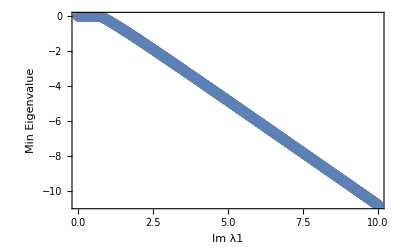

```mathematica
(*Just to visualize -- let us see the Plot with Max's ideas*)


hesNumericalValues = N[hesWithMinima/.{m->-1, λH->1,λS->3, Re[λ1]->1, λP->-10^-6}]//Chop;

sensitivity = Table[
{P, Min[N[Eigenvalues[hesNumericalValues/.{Im[λ1]->P}]//Chop]]},
{P,0,10,10^-2}
];

ListPlot[sensitivity,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Im λ1","Min Eigenvalue"},PlotMarkers->Automatic]
Manipulate[MatrixForm[DiagonalMatrix[hesNumericalValues/.{Im[λ1]->y}]//Chop],{y,0,10}]
```

```mathematica
N[Manipulate[D[hesNumericalValues[[2,2]], Im[λ1]]/.{Im[λ1]->y}, {y,0,3}]]
```

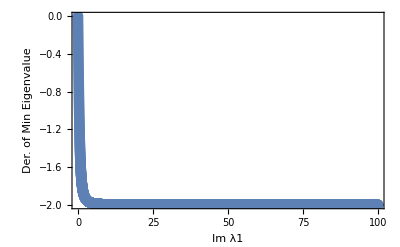

```mathematica
func = Table[
{P, Min[N[Eigenvalues[D[hesNumericalValues, Im[λ1]]/.{Im[λ1]->P}]//Chop]]},
{P,0,100,10^-2}
];

ListPlot[func,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Im λ1","Der. of Min Eigenvalue"},PlotMarkers->Automatic]
```

```mathematica
(*Checking hypothesis of how the stability changes with λS!*)
```

```mathematica
hesNumerical =  N[hesWithMinima/.{m->-1, λH->1, Re[λ1]->1, λP->-10^-6}]//Chop;
```

```mathematica
forLS = Table[
{i, N[hesNumerical/.{λS->i}]},
{i,2,6,1}
];
```

```mathematica
Length[forLS]
```

5

```mathematica
plot2 = Table[
{P, Min[N[forLS[[n,2]]/.{Im[λ1]->P}]//Chop]},
{n, 5},
{P,0,6,0.01}
];
```

```mathematica
Length[plot2]
```

5

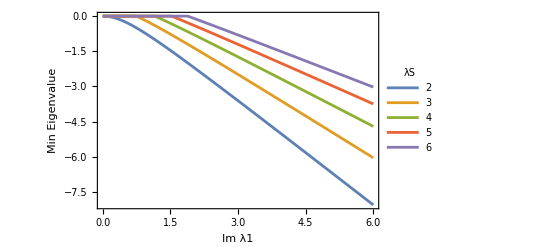

```mathematica
ListPlot[plot2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Im λ1","Min Eigenvalue"},PlotLegends->Placed[LineLegend[forLS[[All,1]],LegendLabel->"λS"],Right]]
```